```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0} 
N3dγ[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
Ntγ[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dγ[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
Ntγ[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nγ[x_]:=Ntγ[x]/Sqrt[Sum[Ntγ[x][[i]] Ntγ[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nγ[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in \Nalba_i \Nabla^i H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] ϕ'[r]
```

```mathematica
(*fVISC[r] = f^{VISC r}_notes*)
```

```mathematica
fVISCt[r_]:=(2 η (v''[r]+(v'[r] z'[r] z''[r])/(1+z'[r]^2)-(2 v[r] z'[r]^2 z''[r]^2)/((1+z'[r]^2)^2)+(v[r] z''[r]^2)/(1+z'[r]^2)+(-v[r]/r+v'[r]+(v[r] z'[r] z''[r])/(1+z'[r]^2))/r+(v[r] z'[r] Derivative[3][z][r])/(1+z'[r]^2)))/(1+z'[r]^2)
```

```mathematica
fσt[r_]:=ig[r][[1,1]]σ'[r]
```

```mathematica
fvt[r_]:=ρ v[r]Δrvr[r]
```

```mathematica
(*d[r][[i,j]] = d_{ij}_notes*)
```

```mathematica
d[r_]:={{g[r][[1,1]]Δrvr[r],0},{0,g[r][[2,2]]Δθvθ[r]}}
```

```mathematica
(*Π[r_][[i,j]]= \Pi^{ij}_notes*)
```

```mathematica
Π[r_]:=Table[Table[-σ[r]ig[r][[i,j]]-2 η ig[r][[i,i]]ig[r][[j,j]]d[r][[i,j]],{j,1,2}],{i,1,2}]
```

```mathematica
(*force per unit length exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdl[r_]:=Table[Sum[Π[r][[i,j]] g[r][[j, k]]*nγ[{r,θ}][[k]],{j,1,2},{k,1,2}],{i,1,2}]
```

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
```

```mathematica
(*Here I pose an exact solution of this kind and compute all resulting quantitites *)
```

```mathematica
z[r_]:=CC * r
```

```mathematica
eqs[[1]]
```

C1^2/((1+CC^2) r^3)+σ'[r]/(1+CC^2)==0

```mathematica
DSolve[eqs[[1]],σ[r],r]
```

{{σ[r]→C1^2/(2 r^2)+C[1]}}

```mathematica
solσ={σ[r]->C1^2/(2 r^2),σ'[r]->-C1^2/r^3};
```

```mathematica
(eqs[[2]]/.solσ//FullSimplify)
```

CC (1+CC^2) (-2+C1^2+(-1+C1^2) CC^2+4 C1 √(1+CC^2))==0

```mathematica
solC1=Solve[ (-2+C1^2+(-1+C1^2) CC^2+4 C1 √(1+CC^2))==0,C1]
```

{{C1→(-2 √(1+CC^2)-√(6+7 CC^2+CC^4))/(1+CC^2)},{C1→(-2 √(1+CC^2)+√(6+7 CC^2+CC^4))/(1+CC^2)}}

```mathematica
C1=(C1/.solC1[[2]])
```

(-2 √(1+CC^2)+√(6+7 CC^2+CC^4))/(1+CC^2)

```mathematica
σRmin=FullSimplify[σ[r]/.solσ,Assumptions->ass]/.{r->Rmin}
```

(10+CC^2-4 √(6+CC^2))/(2 (1+CC^2))

```mathematica
σRmax=FullSimplify[σ[r]/.solσ,Assumptions->ass]/.{r->Rmax}
```

(10+CC^2-4 √(6+CC^2))/(8 (1+CC^2))

```mathematica
v[r]/.repv//FullSimplify
```

(-2 √(1+CC^2)+√(6+7 CC^2+CC^4))/((1+CC^2)^(3/2) r)

```mathematica
(*v^i n_i_{r = Rmax} = v_R_const in variational_problem_bc_ring.py *)
```

```mathematica
FullSimplify[(Sum[{v[r],0}[[i]]* nR[{r,θ}][[j]] g[r][[i,j]],{i,1,2},{j,1,2}])/.repv/.{r->Rmax},Assumptions->ass]
```

(-2+√(6+CC^2))/(2 √(1+CC^2))

```mathematica
H[r]
```

CC/(2 √(1+CC^2) r)

```mathematica
Clear[z]
```

```mathematica
CC=1;
```

```mathematica
bcs={
σ[Rmin]==σRmin,σ[Rmax]==σRmax,
z[Rmin]==CC Rmin,z'[Rmin]==CC,z'[Rmax]==CC
};
```

```mathematica
bcs
```

{σ[1]==1/4 (11-4 √7),σ[2]==1/16 (11-4 √7),z[1]==1,z'[1]==1,z'[2]==1}

```mathematica
Flatten[{eqs,bcs}]
```

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
(*Boundary conditions to feed into the finite-element code*)
```

```mathematica
(*σ[Rmin] = sigma_r_const in variatinal_problem_bc_ring.py*)
```

```mathematica
N[σRmin,20]
```

0.1042486889354094095

```mathematica
(σ[r]/.repv/.sol)/.{r->Rmin}
```

0.10424868893540940949838424636

```mathematica
(*z[Rmin]= z_r_const in variational_problem_bc_ring.py*)
```

```mathematica
z[r]/.{r->Rmin}/.sol
```

1.

```mathematica
(*z[Rmax]= z_R_const in variational_problem_bc_ring.py*)
```

```mathematica
z[r]/.{r->Rmax}/.sol
```

2.0000000000000047500590170641

```mathematica
(*(omega_r at r = Rmin) = omega_r_const in variational_problem_bc_ring.py*)
```

```mathematica
(z'[r]/.repv/.sol)/.{r->Rmin}
```

0.01

```mathematica
(*omega_r at r = Rmax = omega_R_const in variational_problem_bc_ring.py*)
```

```mathematica
(z'[r]/.repv/.sol)/.{r->Rmax}
```

0.011278978419320677350524558049

```mathematica
(*v[Rmin] = v_r_const in variational_problem_bc_ring.py*)
```

```mathematica
v[r]/.repv/.{r->Rmin}/.sol
```

0.4494652085917910938157596

```mathematica
(*v[Rmax] = v_R_const in variational_problem_bc_ring.py*)
```

```mathematica
v[r]/.repv/.{r->Rmax}/.sol
```

0.22472954657536892163115126795934

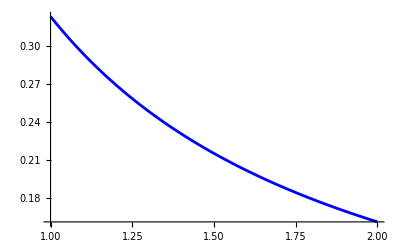

```mathematica
plotvODE=Plot[{v[r]/.repv/.sol},{r,Rmin,Rmax},PlotStyle->Blue]
```

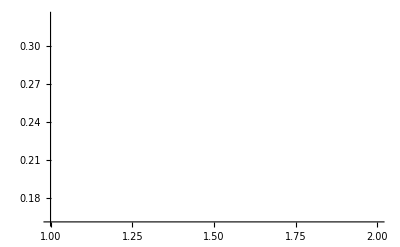

```mathematica
plotvanalytical=Plot[(-2 √(1+CC^2)+√(6+7 CC^2+CC^4))/((1+CC^2)^(3/2) r),{r,Rmin,Rmax},PlotStyle->{Red,Thickness->0.01,Opacity->0.001}]
```

```mathematica
Show[plotvanalytical,plotvODE]
```

-Graphics-

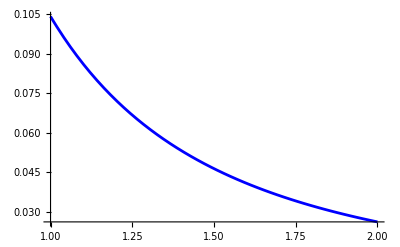

```mathematica
plotσODE=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

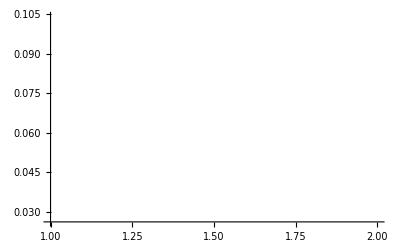

```mathematica
plotσanalytical=Plot[σ[r]/.solσ,{r,Rmin,Rmax},PlotStyle->{Red,Thickness->0.01,Opacity->0.001}]
```

```mathematica
Show[plotσanalytical,plotσODE]
```

-Graphics-

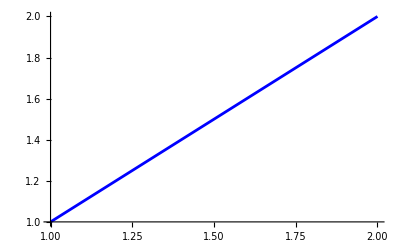

```mathematica
plotzODE=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

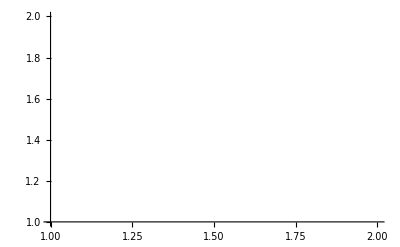

```mathematica
plotzanalytical=Plot[CC r,{r,Rmin,Rmax},PlotRange->All,PlotStyle->{Red,Thickness->0.01,Opacity->0.001}]
```

```mathematica
Show[plotzanalytical,plotzODE]
```

-Graphics-

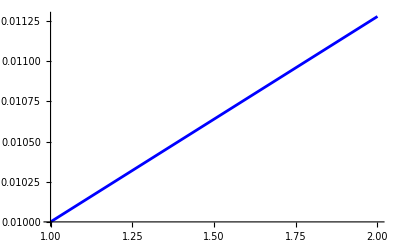

```mathematica
plotωODE=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

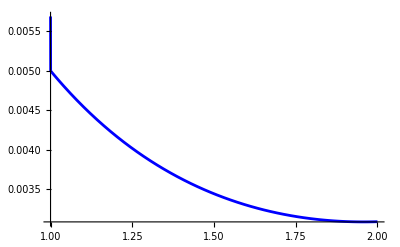

```mathematica
plotμODE=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
delta=1/100;
```

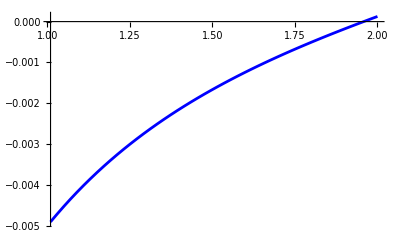

```mathematica
plotνODE=Plot[Evaluate[H'[r]/. sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

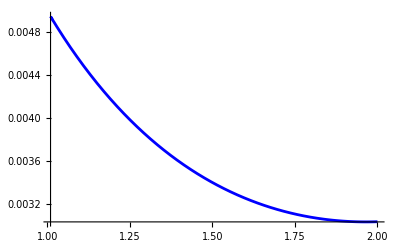

```mathematica
plotτODE=Plot[Evaluate[NablaNablaH[r]/. sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

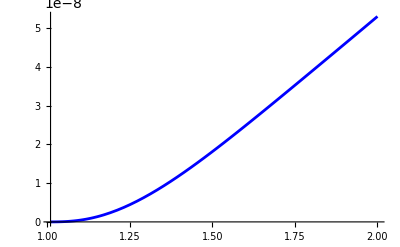

```mathematica
plotfVISCtODE=Plot[Evaluate[fVISCt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

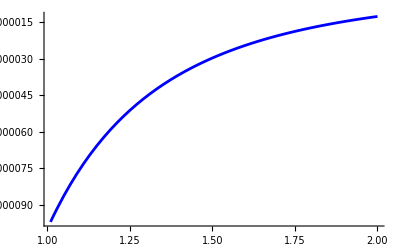

```mathematica
plotfσtODE=Plot[Evaluate[fσt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

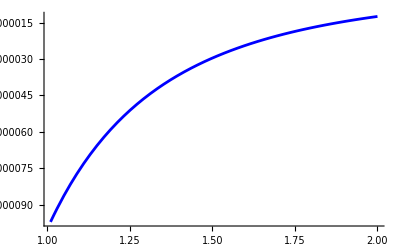

```mathematica
plotfvtODE=Plot[Evaluate[fvt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

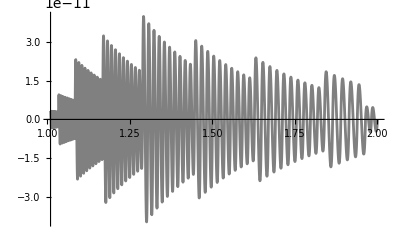

```mathematica
plotftottODE=Plot[Evaluate[(fvt[r]-fσt[r]-fVISCt[r])/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Gray]
```

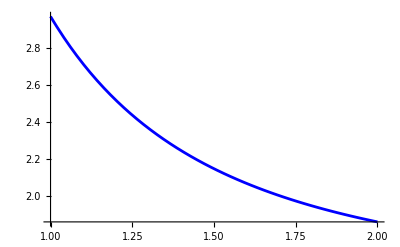

```mathematica
plotdFdlODE=  Plot[Evaluate[dFdl[r][[1]]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

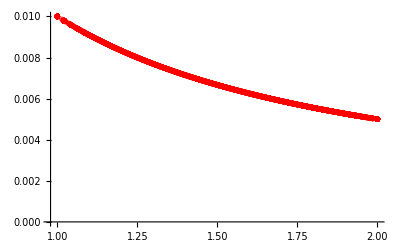

```mathematica
tabv=Import["~/Documents/finite_elements/steady-state-flow/solution/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],({tabv[[i,4]],tabv[[i,5]]}/Norm[{tabv[[i,4]],tabv[[i,5]]}]).{tabv[[i,1]],tabv[[i,2]]}},{i,2,Length[tabv]}]
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

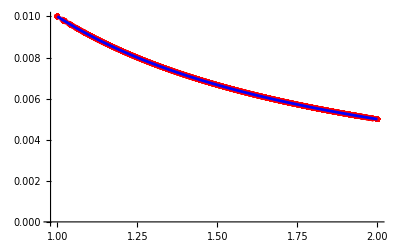

```mathematica
Show[plotvfe,plotvexact]
```

```mathematica
(*check of sigma*)
```

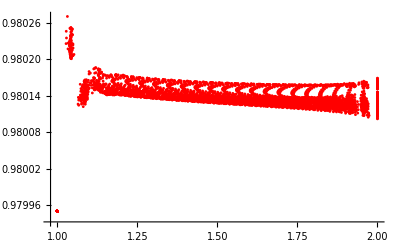

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.005,Red,Opacity[1]}]
```

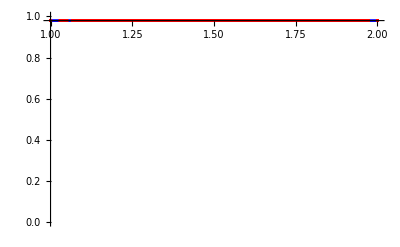

```mathematica
Show[plotσexact,plotσfe,PlotRange->{0,1}]
```

```mathematica
(*check of z*)
```

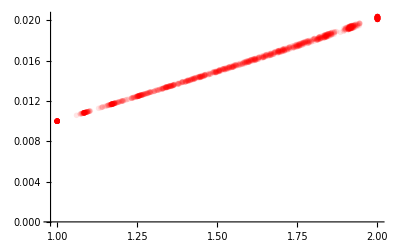

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

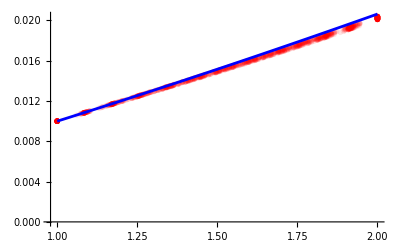

```mathematica
Show[plotzfe,plotzexact]
```

```mathematica
(*check of ω*)
```

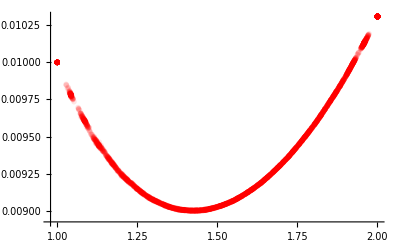

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

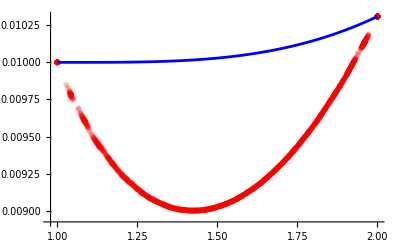

```mathematica
Show[plotωfe,plotωexact]
```

```mathematica
(*check of μ*)
```

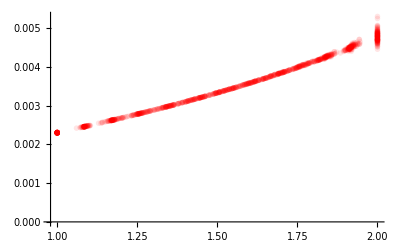

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

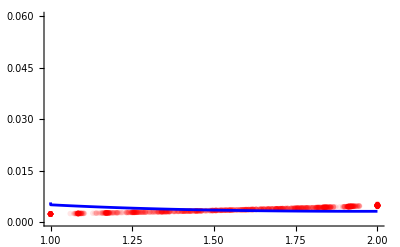

```mathematica
Show[plotμfe,plotμexact,PlotRange->{0,0.06}]
```

```mathematica
(*check nu*)
```

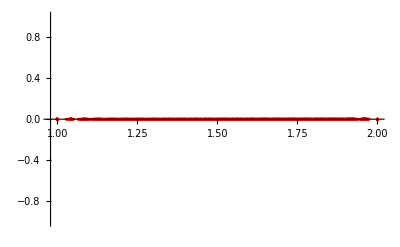

```mathematica
ν=Import["~/Documents/finite_elements/steady-state-flow/solution/nu.csv"];
ν=Table[{Sqrt[ν[[i,4]]^2+ν[[i,5]]^2],ν[[i,4]]/Sqrt[ν[[i,4]]^2+ν[[i,5]]^2] ν[[i,1]]+ν[[i,5]]/Sqrt[ν[[i,4]]^2+ν[[i,5]]^2] ν[[i,2]]},{i,2,Length[ν]}]
plotνnum=ListPlot[ν,PlotStyle->{Red,Opacity->1}]
```

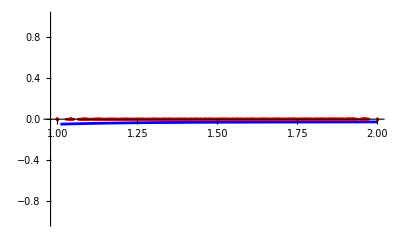

```mathematica
Show[plotνnum,plotνexact]
```

```mathematica
(*check τ*)
```

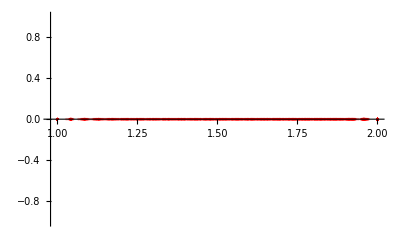

```mathematica
τnum=Import["~/Documents/finite_elements/steady-state-flow/solution/tau.csv"];
τnum=Table[{Sqrt[τnum[[i,2]]^2+τnum[[i,3]]^2],τnum[[i,1]]},{i,2,Length[τnum]}]
plotτnum=ListPlot[τnum,PlotStyle->{Red,Opacity->0.1}]
```

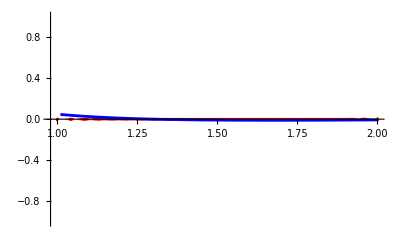

```mathematica
Show[plotτnum,plotτexact]
```

```mathematica
(*check of forces*)
```

```mathematica
(*normal forces*)
```

```mathematica
tabfeln=Import["~/Documents/finite_elements/steady-state-flow/solution/fel_n.csv"];
tabfeln=Table[{Norm[{tabfeln[[i,2]],tabfeln[[i,3]]}],tabfeln[[i,1]]},{i,2,Length[tabfeln]}]
```

```mathematica
tabflaplacen=Import["~/Documents/finite_elements/steady-state-flow/solution/flaplace.csv"];
tabflaplacen=Table[{Norm[{tabflaplacen[[i,2]],tabflaplacen[[i,3]]}],tabflaplacen[[i,1]]},{i,2,Length[tabflaplacen]}]
```

```mathematica
tabfviscn=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_n.csv"];
tabfviscn=Table[{Norm[{tabfviscn[[i,2]],tabfviscn[[i,3]]}],tabfviscn[[i,1]]},{i,2,Length[tabfviscn]}]
```

```mathematica
tabftotn=Table[{tabfviscn[[i,1]],tabfeln[[i,2]]+tabflaplacen[[i,2]]+tabfviscn[[i,2]]},{i,2,Length[tabfviscn]}]
```

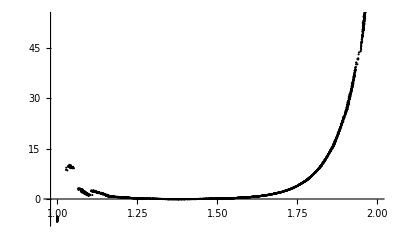

```mathematica
ListPlot[tabftotn,PlotStyle->Black]
```

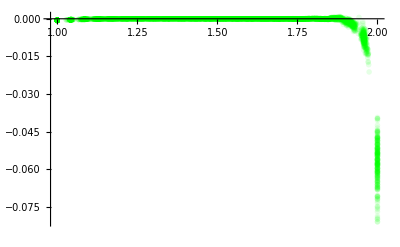

```mathematica
plotfeln=ListPlot[tabfeln,PlotRange->Full,PlotStyle->{PointSize->.01,Green,Opacity[0.1]}]
```

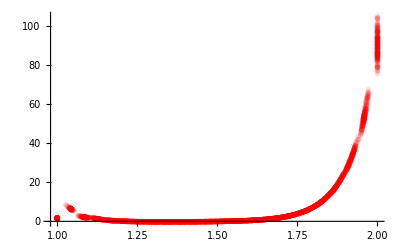

```mathematica
plotflaplacen=ListPlot[tabflaplacen,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

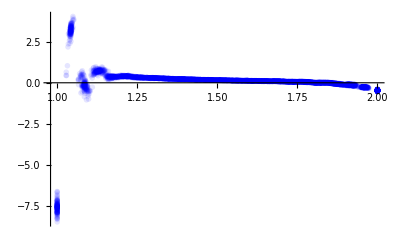

```mathematica
plotfviscn=ListPlot[tabfviscn,PlotRange->Full,PlotStyle->{PointSize->.01,Blue,Opacity[0.1]}]
```

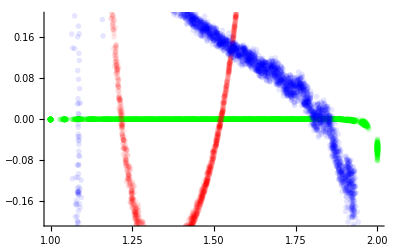

```mathematica
Show[plotfeln,plotflaplacen,plotfviscn,PlotRange->{-0.2,0.2}]
```

```mathematica
(*tangential forces*)
```

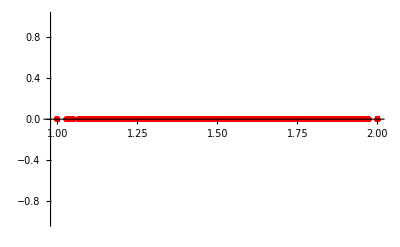

```mathematica
tabfVISCt=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv"];
tabfVISCt=Table[{Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}],({tabfVISCt[[i,4]],tabfVISCt[[i,5]]}/Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}]).{tabfVISCt[[i,1]],tabfVISCt[[i,2]]}},{i,2,Length[tabfVISCt]}]
plotfVISCtfe=ListPlot[tabfVISCt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[1]}]
```

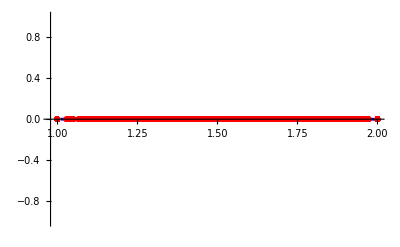

```mathematica
Show[plotfVISCtfe,plotfVISCtexact]
```

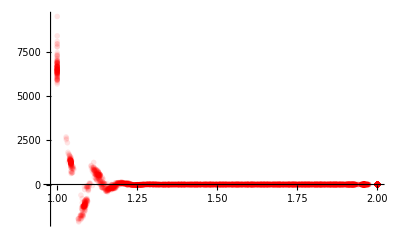

```mathematica
tabfσt=Import["~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv"];
tabfσt=Table[{Norm[{tabfσt[[i,4]],tabfσt[[i,5]]}],({tabfσt[[i,4]],tabfσt[[i,5]]}/Norm[{tabfσt[[i,4]],tabfσt[[i,5]]}]).{tabfσt[[i,1]],tabfσt[[i,2]]}},{i,2,Length[tabfσt]}]
plotfσtfe=ListPlot[tabfσt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

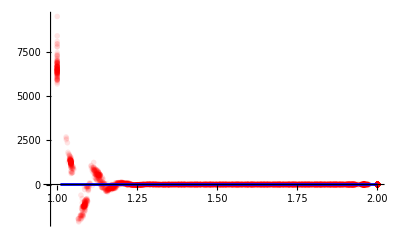

```mathematica
Show[plotfσtfe,plotfσtexact]
```

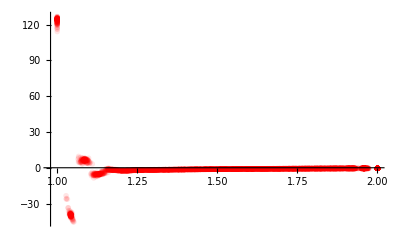

```mathematica
tabfvt=Import["~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv"];
tabfvt=Table[{Norm[{tabfvt[[i,4]],tabfvt[[i,5]]}],({tabfvt[[i,4]],tabfvt[[i,5]]}/Norm[{tabfvt[[i,4]],tabfvt[[i,5]]}]).{tabfvt[[i,1]],tabfvt[[i,2]]}},{i,2,Length[tabfvt]}]
plotfvtfe=ListPlot[tabfvt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

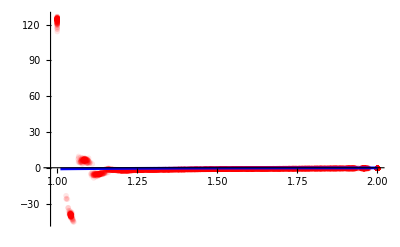

```mathematica
Show[plotfvtfe,plotfvtexact]
```

```mathematica
(*check that the sum fVISCt + fσt- fvt = 0*)
```

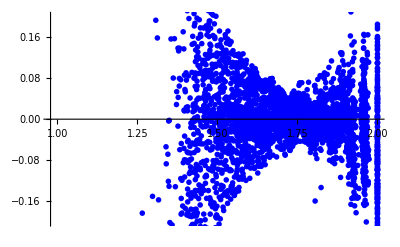

```mathematica
tabfVISCt=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv"];
tabfσt=Import["~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv"];
tabfvt=Import["~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv"];
tabftott=Table[{Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}],({tabfVISCt[[i,4]],tabfvt[[i,5]]}/Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}]).{tabfVISCt[[i,1]]+tabfσt[[i,1]]-tabfvt[[i,1]],tabfVISCt[[i,2]]+tabfσt[[i,2]]-tabfvt[[i,2]]}},{i,2,Length[tabfVISCt]}]
plotftottfe=ListPlot[tabftott,PlotRange->{-0.2,0.2},PlotStyle->{PointSize->.01,Blue,Opacity[1]}]
```

```mathematica
(*res = 0.1*)
```

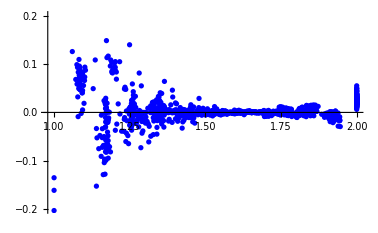
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.05*)
```

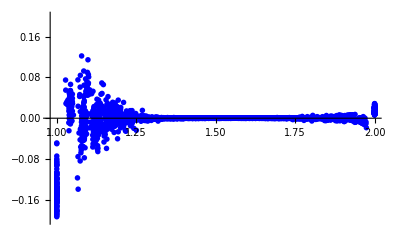
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.02*)
```

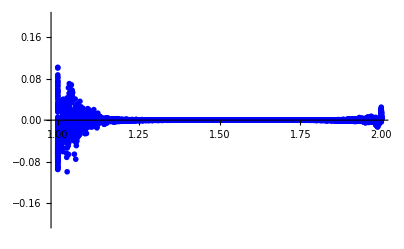
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.01*)
```

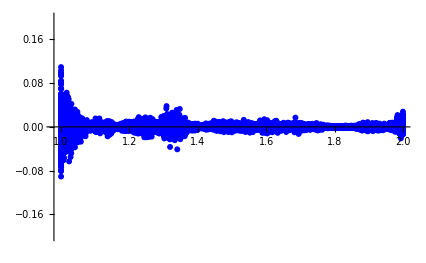
```mathematica
-Graphics-;
```

```mathematica
(*force exerted on a line element, dFdl*)
```

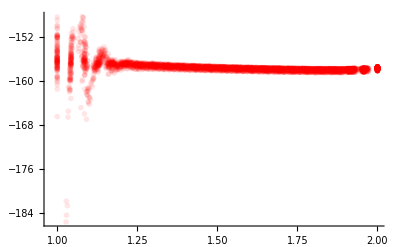

```mathematica
tabdFdl=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl.csv"];
tabdFdl=Table[{Norm[{tabdFdl[[i,4]],tabdFdl[[i,5]]}],({tabdFdl[[i,4]],tabdFdl[[i,5]]}/Norm[{tabdFdl[[i,4]],tabdFdl[[i,5]]}]).{tabdFdl[[i,1]],tabdFdl[[i,2]]}},{i,2,Length[tabdFdl]}]
plotdFdlfe=ListPlot[tabdFdl,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

```mathematica
Show[plotdFdlfe,plotdFdlexact]
```

-Graphics-

```mathematica
(*res = 0.1*)
```

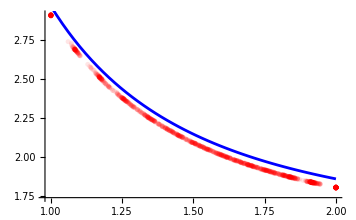
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.05*)
```

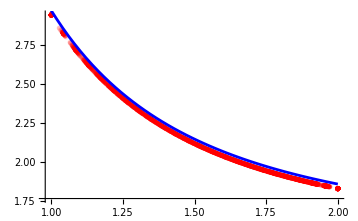
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.02*)
```

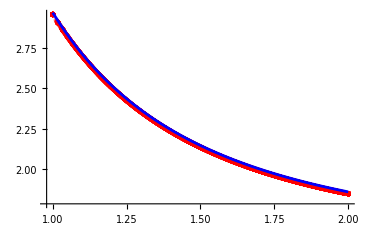
```mathematica
-Graphics-;
```

```mathematica
(*res = 0.01*)
```

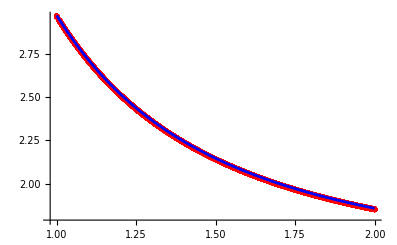
```mathematica
-Graphics-;
```